```mathematica
Integrate[ⅇ^(-ⅈ (k-x) x),{x,0,∞},Assumptions->k∈Reals]
```

(1/2+ⅈ/2) ⅇ^(-(ⅈ k^2)/4) √(π/2) (1+(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])

```mathematica
f[k_]:=Abs[(1/2+ⅈ/2) ⅇ^(-(ⅈ k^2)/4) √(π/2) (1+(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])]
```

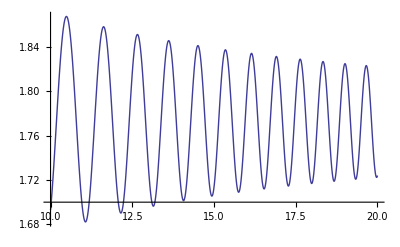

```mathematica
Plot[f[x],{x,10,20}]
```

```mathematica
Integrate[ⅇ^(-ⅈ (k+x) x),{x,0,∞},Assumptions->k∈Reals]
```

(1/2+ⅈ/2) ⅇ^((ⅈ k^2)/4) √(π/2) (-ⅈ-(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])

```mathematica
g[k_]:=Abs[(1/2+ⅈ/2) ⅇ^((ⅈ k^2)/4) √(π/2) (-ⅈ-(1-ⅈ) FresnelC[k/(√(2 π))]+(1+ⅈ) FresnelS[k/(√(2 π))])]
```

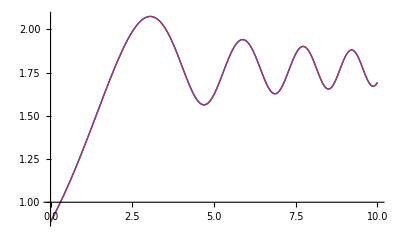

```mathematica
Plot[{f[x],g[-x]},{x,0,10}]
```

```mathematica
FindMinimum[{f[x],14.900000000000000000000<=x≤15.000000000000000000000},{x,14.935},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->20]
```

FindMinimum::precw: The precision of the argument function ({{14.9`22.173186268412277 ≤ x, x ≤ 15.`22.176091259055685}}) is less than WorkingPrecision (20.).

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 507 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.00010171684529544471`, 0.`, 0.0000508584231208069`}, is returned.

{1.70551,{x→14.935}}